# e^-e^+→ μ^-μ^+

## Feynman Diagram



```mathematica
R1=CreateTopologies[0, 2 -> 2];
Paint[%];
```

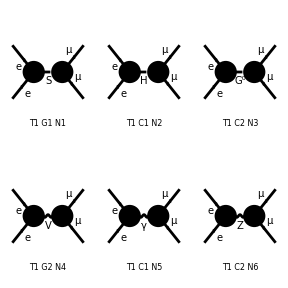

```mathematica
S1=CreateTopologies[0, 2 -> 2];
diags1= InsertFields[R1, {-F[2, {1}], F[2, {1}]} ->
		{-F[2, {2}], F[2, {2}]}];
Paint[%];
```

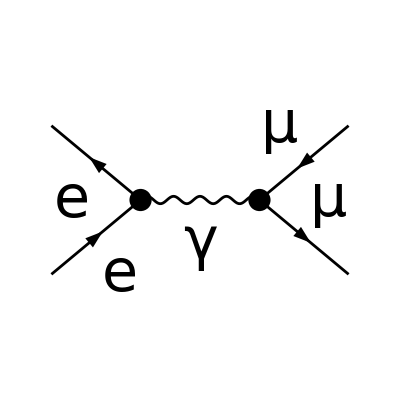

```mathematica
T1=CreateTopologies[0, 2 -> 2];
diagt1 = InsertFields[T1, {-F[2, {1}], F[2, {1}]} ->
		{-F[2, {2}], F[2, {2}]}, InsertionLevel -> {Classes},
		Model -> "SM", ExcludeParticles -> {S[1], S[2], V[2]}];
Paint[diagt1, ColumnsXRows -> {1, 1}, Numbering -> None,SheetHeader->None,ImageSize->{512,512}];
```

## Square amplitude (Momenta)

```mathematica
A = FCFAConvert[CreateFeynAmp[diagt1, Truncated -> False],
IncomingMomenta->{p,p'},OutgoingMomenta->{k,k'},UndoChiralSplittings->True,
ChangeDimension->4,List->False,SMP->True]
```

((ḡ)^Lor1Lor2 (φ(-p̄,m_e)).(ⅈ e (γ̄)^Lor1).(φ(OverBar[p'],m_e)) (φ(OverBar[k'],m_μ)).(ⅈ e (γ̄)^Lor2).(φ(-k̄,m_μ)))/(k̄+OverBar[k'])^2

```mathematica
ComplexConjugate[A]
```

-(e^2 (ḡ)^Lor1Lor2 (φ(OverBar[p'],m_e)).(γ̄)^Lor1.(φ(-p̄,m_e)) (φ(-k̄,m_μ)).(γ̄)^Lor2.(φ(OverBar[k'],m_μ)))/(OverBar[k']+k̄)^2

```mathematica
sqAmp =ChangeDimension[(A (ComplexConjugate[A]//FCRenameDummyIndices))//Contract//FermionSpinSum[#, ExtraFactor -> 1/4]&//
		ReplaceAll[#, DiracTrace :> Tr]&//Contract//FullSimplify, D]
```

8 e^4 (1/(k+k')^2)^2 (m_e^2 (k·k')+m_μ^2 (2 m_e^2+p·p')+(k·p') (p·k')+(k·p) (k'·p'))

```mathematica
masslessElectronssqAmp= (sqAmp/. {SMP["m_e"] -> 0}/.{Momentum[k,D]+Momentum[k',D]->q})//FullSimplify
```

8 e^4 (1/(k+k')^2)^2 ((k·p') (p·k')+(k·p) (k'·p')+m_μ^2 (p·p'))

```mathematica
AllmasslessqAmp= (masslessElectronssqAmp/. {SMP["m_mu"] -> 0})//FullSimplify
```

8 e^4 (1/(k+k')^2)^2 ((k·p') (p·k')+(k·p) (k'·p'))

## Kinematics

Incoming Momenta - p (electron), p’(positron)

p^μ=(p^0,p^1,p^2,p^3)
p_e=(E_e, 0, 0, p_e z )
p'_p=(E_p, 0, 0, -p_ez )
Invariant: p_e^2=E_e^2-m_e^2

Outgoing Momenta - k (muon), k’ (anti-muon)

k^μ=(k^0,k^1,k^2,k^3)
k_μ=(E_μ, k_μ x, k_μ y, k_μ z )=(E_μ, k )
k'_(μ+)=(E_(μ+), -k_(μ+)x, -k_(μ+)y,- k_(μ+)z )=(E_μ, -k )
Invariant: k_μ^2=E_μ^2-m_μ^2

General:
s = ( p^μ+p'^μ )^2 =( k^μ+k'^μ )^2 = (p)^2+(p')^2+2( p*p' ) = (p^0)^2-p^2+(p'^0)^2-p'^2+2 p^0 p'^0-2p p'cos( θ ) 

t = ( k^μ-p^μ )^2 = ( k'^μ-p'^μ )^2 = (k)^2+(p)^2-2( k*p ) = (k^0)^2-k^2+(p^0)^2-p^2-2 k^0 p^0+2k p cos( θ )

u = ( k'^μ-p^μ )^2 = ( k^μ-p'^μ )^2 = (k')^2+(p)^2+2( k'*p ) = (k'^0)^2-k'^2+(p^0)^2-p^2-2 k'^0 p^0+2k' p cos( θ )

```mathematica
Inputs
```

Inputs

```mathematica
p0=Ee;
p1=0;
p2=0;
p3=Subscript[p, e];
pp0=Ee;
pp1=0;
pp2=0;
pp3=-Subscript[p, e];
k0=Eμ;
k1=kx;
k2=ky;
k3=kz;
kp0=Eμ;
kp1=-kx;
kp2=-ky;
kp3=-kz;
θz=0;
θ=θ;
```

```mathematica
g=({{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}});
```

```mathematica
pdotpp=Inner[Times,{p0,p1,p2,p3},Inner[Times,g,{pp0,pp1,pp2,pp3},Plus],Plus]
kdotkp=Inner[Times,{k0,k1,k2,k3},Inner[Times,g,{kp0,kp1,kp2,kp3},Plus],Plus]
kdotp=Inner[Times,{k0,k1,k2,k3},Inner[Times,g,{p0,p1,p2,p3},Plus], Plus]
kpdotpp=Inner[Times,{kp0,kp1,kp2,kp3},Inner[Times,g,{pp0,pp1,pp2,pp3},Plus],Plus]
kpdotp=Inner[Times,{kp0,kp1,kp2,kp3},Inner[Times,g,{p0,p1,p2,p3},Plus],Plus]
kdotpp=Inner[Times,{k0,k1,k2,k3},Inner[Times,g,{pp0,pp1,pp2,pp3},Plus],Plus]
zhat=cos[θ]
```

p_e^2+Ee^2

Eμ^2+kx^2+ky^2+kz^2

Ee Eμ-kz p_e

Ee Eμ-kz p_e

kz p_e+Ee Eμ

kz p_e+Ee Eμ

cos(θ)

```mathematica
mass1=0;
mass2=Subscript[m, μ];
E1=Ee;
E2=Emu;
E3=Ee;
E4=Eμ;

Subscript[p, e]=√(E1^2-mass1^2)//PowerExpand
Subscript[k, μ]=√(E2^2-mass2^2)//PowerExpand
|p|=√(E3^2-mass1^2)//PowerExpand
|k|=√(E4^2-mass2^2)//PowerExpand
|p'|=-|p|;
|k'|=-|k|;
kz=|k|zhat;
```

Ee

√(Emu^2-m_μ^2)

Ee

√(Eμ^2-m_μ^2)

```mathematica
pdotpp
kdotp
kpdotp
```

2 Ee^2

Ee Eμ-Ee cos(θ) √(Eμ^2-m_μ^2)

Ee cos(θ) √(Eμ^2-m_μ^2)+Ee Eμ

```mathematica
schannel=p0^2-(|p|)^2+pp0^2-(|p'|)^2+2*p0*pp0-2*|p|*|p'|*Cos[θz]

tchannel=k0^2-(|k|)^2+p0^2-(|p|)^2-2*k0*p0+2*|k|*|p|*Cos[θ]

uchannel=kp0^2-(|k'|)^2+p0^2-(|p|)^2-2*kp0*p0+2*|k'|*|p|*Cos[θ]
```

4 Ee^2

2 Ee cos(θ) √(Eμ^2-m_μ^2)-2 Ee Eμ+m_μ^2

-2 Ee cos(θ) √(Eμ^2-m_μ^2)-2 Ee Eμ+m_μ^2

## Cross Section

```mathematica
|Subscript[v, A]-Subscript[v, B]|=2;
EA=EB=Ecm/2;
SPD[p',k']=SPD[p,k];
SPD[p',k]=SPD[p,k'];
SPD[p,k]= kdotp;
SPD[p,k']= kpdotp;
SPD[p,p']= pdotpp;
q=(schannel)^(1/2);
Clear[θ]
DiffCross=(d[Cos θ]dϕ)/(2EA 2 EB|Subscript[v, A]-Subscript[v, B]|)(|k|)/(4 π^2 4Ecm)*masslessElectronssqAmp//FullSimplify
```

(dϕ e^4 Ee^2 (1/(4 Ee^2))^2 d(Cos θ) √(Eμ^2-m_μ^2) ((cos(θ))^2 (Eμ^2-m_μ^2)+Eμ^2+m_μ^2))/(2 π^2 Ecm^3)

```mathematica
DiffCross/(d[Cos θ]dϕ)
```

(e^4 Ee^2 (1/(4 Ee^2))^2 √(Eμ^2-m_μ^2) ((cos(θ))^2 (Eμ^2-m_μ^2)+Eμ^2+m_μ^2))/(2 π^2 Ecm^3)

```mathematica
R=(e^4 Ee^2)/schannel^2(√(Eμ^2-Subscript[m, μ]^2)(Cos[θ]^2(Eμ^2-Subscript[m, μ]^2)+Eμ^2+Subscript[m, μ]^2))/(2 π^2 Ecm^3);
```

```mathematica
R/(Cos[θ]^2(Eμ^2- Subscript[m, μ]^2)+Subscript[m, μ]^2+Eμ^2)
```

(e^4 √(Eμ^2-m_μ^2))/(32 π^2 Ecm^3 Ee^2)

```mathematica
%*(Eμ^2*((1-Subscript[m, μ]^2/Eμ^2)Cos[θ]^2+(1+Subscript[m, μ]^2/Eμ^2)))
```

(e^4 Eμ^2 √(Eμ^2-m_μ^2) (cos^2(θ) (1-m_μ^2/Eμ^2)+m_μ^2/Eμ^2+1))/(32 π^2 Ecm^3 Ee^2)

```mathematica
Ee=Eμ;
```

```mathematica
CrossSection=e^4 Eμ^2 1/(32 π^2 Ecm^3 Ee^2)(Eμ)PowerExpand[√(Distribute[1/Eμ^2(Eμ^2-Subscript[m, μ]^2)])]((Subscript[m, μ]^2/Eμ^2+1)+Cos[θ]^2(1-Subscript[m, μ]^2/Eμ^2))
```

(e^4 Eμ √(1-m_μ^2/Eμ^2) (cos^2(θ) (1-m_μ^2/Eμ^2)+m_μ^2/Eμ^2+1))/(32 π^2 Ecm^3)

```mathematica
e=√(4π α);
Eμ=Eτ;
```

```mathematica
dσ/dΩ==CrossSection*EA/Eμ
```

dσ/dΩ==(α^2 √(1-m_μ^2/Eτ^2) (cos^2(θ) (1-m_μ^2/Eτ^2)+m_μ^2/Eτ^2+1))/(4 Ecm^2)

## Total Cross Section

```mathematica
Eτ=Eg;
dϕ=2π;
```

```mathematica
W=CrossSection*EA/Eμ*dϕ
```

(π α^2 √(1-m_μ^2/Eg^2) (cos^2(θ) (1-m_μ^2/Eg^2)+m_μ^2/Eg^2+1))/(2 Ecm^2)

```mathematica
Integrate[W, {Cos[θ],0,π}]
```

Integrate::ivar: cos(θ) is not a valid variable.

∫_0^π (π α^2 √(1-m_μ^2/Eg^2) (cos^2(θ) (1-m_μ^2/Eg^2)+m_μ^2/Eg^2+1))/(2 Ecm^2)ⅆcos(θ)

```mathematica
(π α^2)/(2 Ecm^2)√(1-Subscript[m, μ]^2/Eg^2)((1-Subscript[m, μ]^2/Eg^2)*∫_0^π Cos[θ]^2 Sin[θ]ⅆθ+(1+Subscript[m, μ]^2/Eg^2)*∫_0^π Sin[θ]ⅆθ)//Simplify
```

(2 π α^2 (2 Eg^2+m_μ^2) √(1-m_μ^2/Eg^2))/(3 Ecm^2 Eg^2)

```mathematica
Subscript[σ, total]==(2 π α^2 2 Eg^2(Distribute[1/(2 Eg^2)(2 Eg^2+Subscript[m, μ]^2)]) √(1-Subscript[m, μ]^2/Eg^2))/(3 Ecm^2 Eg^2)
```

σ_total==(4 π α^2 √(1-m_μ^2/Eg^2) (m_μ^2/(2 Eg^2)+1))/(3 Ecm^2)

```mathematica
At High Energies: E >>Subscript[m, μ]-> 0,
```

```mathematica
a=(Series[√(1-(z)^2),{z,0,4}]*((1+1/2 z^2)))
```

1-(3 z^4)/8+O(z^5)

```mathematica
z=Subscript[m, μ]/Eg;
```

```mathematica
Subscript[σ, total]==(4 π α^2)/(3 Ecm^2)*a
```

SeriesData::sdatv: First argument m_μ/Eg is not a valid variable.

σ_total==(4 π α^2 (1-3/8 (m_μ/Eg)^4+O((m_μ/Eg)^5)))/(3 Ecm^2)

## Square Amplitude (Mandelstam)

```mathematica
Clear[p0,p1,p2,p3,pp0,pp1,pp2,pp3,k0,k1,k2,k3,kp0,kp1,kp2,kp3]
```

```mathematica
B = FCFAConvert[CreateFeynAmp[diagt1, Truncated -> False],
IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},UndoChiralSplittings->True,
ChangeDimension->4,List->False,SMP->True]
```

((ḡ)^Lor1Lor2 (φ(-OverBar[p1],m_e)).(ⅈ e (γ̄)^Lor1).(φ(OverBar[p2],m_e)) (φ(OverBar[k2],m_μ)).(ⅈ e (γ̄)^Lor2).(φ(-OverBar[k1],m_μ)))/(OverBar[k1]+OverBar[k2])^2

```mathematica
SetMandelstam[s, t, u, p1, p2, -k1, -k2, SMP["m_e"], SMP["m_e"], SMP["m_mu"], SMP["m_mu"]];
sqAmpM =(B(ComplexConjugate[B]//FCRenameDummyIndices))//PropagatorDenominatorExplicit//Contract//FermionSpinSum[#, ExtraFactor -> 1/4]&//
		ReplaceAll[#, DiracTrace :> Tr]&//Contract//Simplify
```

(2 e^4 (2 m_e^2 (2 m_μ^2+s-t-u)+2 m_e^4+2 m_μ^4+2 m_μ^2 (s-t-u)+t^2+u^2))/s^2

```mathematica
masslessElectronssqAmpmandel= (sqAmpM/. {SMP["m_e"] -> 0})//FullSimplify
masslessElecMuonsqAmpmandel= (masslessElectronssqAmpmandel/. {SMP["m_mu"] -> 0})//Simplify
```

(2 e^4 (2 m_μ^4-2 m_μ^2 (-s+t+u)+t^2+u^2))/s^2

(2 e^4 (t^2+u^2))/s^2

## Square Amplitude (Mandelstam, Flipped Particles) Test

```mathematica
SetMandelstam[s, t, u, p, p', -k, -k', SMP["m_mu"], SMP["m_mu"], SMP["m_e"], SMP["m_e"]];
sqAmpM2 =(B(ComplexConjugate[B]//FCRenameDummyIndices))//PropagatorDenominatorExplicit//Contract//FermionSpinSum[#, ExtraFactor -> 1/4]&//
		ReplaceAll[#, DiracTrace :> Tr]&//Contract//Simplify
```

(2 e^4 (2 m_e^2 (6 m_μ^2+s-t-u)-2 m_e^4-2 m_μ^4+2 m_μ^2 (s-t-u)+t^2+u^2))/s^2

```mathematica
masslessElectronssqAmpmandel= (sqAmpM2/. {SMP["m_e"] -> 0})//FullSimplify
masslessElecMuonsqAmpmandel= (masslessElectronssqAmpmandel/. {SMP["m_mu"] -> 0})//FullSimplify
```

(2 e^4 (-2 m_μ^2 (m_μ^2-s+t+u)+t^2+u^2))/s^2

(2 e^4 (t^2+u^2))/s^2

## Cross Section (Mandelstam)

```mathematica
|Subscript[v, A]-Subscript[v, B]|=2;
EA=EB=Ecm/2;
SPD[p',k']=SPD[p,k];
SPD[p',k]=SPD[p,k'];
SPD[p,k]= kdotp;
SPD[p,k']= kpdotp;
SPD[p,p']= pdotpp;
q=(schannel)^(1/2);
Clear[θ]
dϕ=.
SigmaM=(d[Cos θ]dϕ)/(2EA 2 EB|Subscript[v, A]-Subscript[v, B]|)(|k|)/(4 π^2 4Ecm)*masslessElecMuonsqAmpmandel//FullSimplify
```

(dϕ e^4 (t^2+u^2) d(Cos θ) √(Eg^2-m_μ^2))/(16 π^2 Ecm^3 s^2)

```mathematica
SigmaM/(d[Cos θ]dϕ)
```

(e^4 (t^2+u^2) √(Eg^2-m_μ^2))/(16 π^2 Ecm^3 s^2)

```mathematica
%//StandardForm
```

((t^2+u^2) SMP[e]^4 √(Eg^2-m_μ^2))/(16 Ecm^3 π^2 s^2)

```mathematica
SMP["e"]=√(4π α);
Eμ=Eg;
(SigmaM/(d[Cos θ]dϕ)/.{SMP["e"]->√(4π α)})
```

Set::write: Tag SMP in e is Protected.

(α^2 (t^2+u^2) √(Eg^2-m_μ^2))/(Ecm^3 s^2)

```mathematica
%//StandardForm
```

((t^2+u^2) α^2 √(Eg^2-m_μ^2))/(Ecm^3 s^2)

```mathematica
((t^2+u^2) α^2 Eg √Distribute[1/Eg^2(Eg^2-Subscript[m, μ]^2)])/(Ecm^3 s^2)/.{Eg->Ecm}
```

(α^2 (t^2+u^2) √(1-m_μ^2/Ecm^2))/(Ecm^2 s^2)

```mathematica
%//StandardForm
```

((t^2+u^2) α^2 √(1-m_μ^2/Ecm^2))/(Ecm^2 s^2)

```mathematica
Eμ=.
```

```mathematica
Mandelcross=1/Ecm^2 Distribute[1/s^2*(t^2+u^2)] α^2 √(1-Subscript[m, μ]^2/Ecm^2)/.{Ecm->Eμ}
```

(α^2 √(1-m_μ^2/Eμ^2) (t^2/s^2+u^2/s^2))/Eμ^2

```mathematica
Denominator[%]/.{Eμ->s}
```

s^2

```mathematica
Y=Mandelcross*1/%*Eμ^2
```

(α^2 √(1-m_μ^2/Eμ^2) (t^2/s^2+u^2/s^2))/s^2

```mathematica
b=(Series[√(1-(w)^2),{w,0,4}])
dϕ=2π;
```

1-w^2/2-w^4/8+O(w^5)

```mathematica
dσ/(d cos[θ])==dϕ*Y*b/.{w->Subscript[m, μ]/Eμ}
```

SeriesData::sdatv: First argument m_μ/Eμ is not a valid variable.

dσ/(d cos(θ))==(2 π α^2 √(1-m_μ^2/Eμ^2) (t^2/s^2+u^2/s^2))/s^2-(π α^2 √(1-m_μ^2/Eμ^2) (m_μ/Eμ)^2 (t^2/s^2+u^2/s^2))/s^2-((m_μ/Eμ)^4 (π α^2 √(1-m_μ^2/Eμ^2) (t^2/s^2+u^2/s^2)))/(4 s^2)+O((m_μ/Eμ)^5)

```mathematica
MultiplySides[%,s]
```

Piecewise[{{(dσ s)/(d cos(θ))==s ((2 π (t^2/s^2+u^2/s^2) α^2 √(1-m_μ^2/Eμ^2))/s^2-(π (t^2/s^2+u^2/s^2) α^2 √(1-m_μ^2/Eμ^2) (m_μ/Eμ)^2)/s^2-((π (t^2/s^2+u^2/s^2) α^2 √(1-m_μ^2/Eμ^2)) (m_μ/Eμ)^4)/(4 s^2)+O((m_μ/Eμ)^5)), s≠0}, {dσ/(d cos(θ))==(2 π α^2 √(1-m_μ^2/Eμ^2) (t^2/s^2+u^2/s^2))/s^2-(π α^2 √(1-m_μ^2/Eμ^2) (m_μ/Eμ)^2 (t^2/s^2+u^2/s^2))/s^2-((m_μ/Eμ)^4 (π α^2 √(1-m_μ^2/Eμ^2) (t^2/s^2+u^2/s^2)))/(4 s^2)+O((m_μ/Eμ)^5), True}}]

## Plot (Cross Section)

```mathematica
Eμ=.;
```

```mathematica
CrossSection*EA/Eμ/.{Eg->Eμ}
```

(α^2 √(1-m_μ^2/Eμ^2) (cos^2(θ) (1-m_μ^2/Eμ^2)+m_μ^2/Eμ^2+1))/(4 Ecm^2)

```mathematica
%//StandardForm
```

(α^2 √(1-m_μ^2/Eμ^2) (1+m_μ^2/Eμ^2+Cos[θ]^2 (1-m_μ^2/Eμ^2)))/(4 Ecm^2)

```mathematica
K1=1-Subscript[m, μ]^2/Eμ^2
K2=1+Subscript[m, μ]^2/Eμ^2
√K1*K1
√K1*K2//Expand
%//Simplify
```

1-m_μ^2/Eμ^2

m_μ^2/Eμ^2+1

(1-m_μ^2/Eμ^2)^(3/2)

(m_μ^2 √(1-m_μ^2/Eμ^2))/Eμ^2+√(1-m_μ^2/Eμ^2)

((Eμ^2+m_μ^2) √(1-m_μ^2/Eμ^2))/Eμ^2

```mathematica
PlotCross=(√K1*K2//Expand//Simplify)+√K1*K1*Z^2
```

((Eμ^2+m_μ^2) √(1-m_μ^2/Eμ^2))/Eμ^2+Z^2 (1-m_μ^2/Eμ^2)^(3/2)

```mathematica
Subscript[m, μ]=105;
Eμ=200;
```

```mathematica
PlotCross
```

(1159 √1159 Z^2)/64000+(2041 √1159)/64000

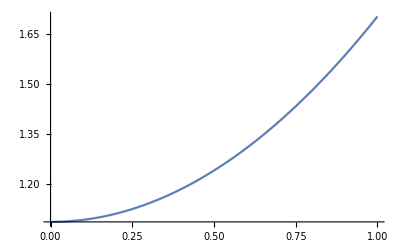

```mathematica
Plot[%,{Z,0,1}]
```

## Plot (Total Cross Section, High Energy)

```mathematica
Subscript[m, μ]=.
```

```mathematica
(4 π α^2)/(3 Ecm^2)*a
```

SeriesData::sdatv: First argument m_μ/Eg is not a valid variable.

(4 π α^2 (1-3/8 (m_μ/Eg)^4+O((m_μ/Eg)^5)))/(3 Ecm^2)

```mathematica
%//StandardForm
```

(4 π α^2 (1-3/8 (m_μ/Eg)^4+O[m_μ/Eg]^5))/(3 Ecm^2)

```mathematica
(Ecm^2).σ==(4 π α^2)/3 (1-3/8 (Subscript[m, μ]/Eg)^4)
```

Ecm^2.σ==4/3 π α^2 (1-(3 m_μ^4)/(8 Eg^4))

## Scratch

```mathematica
k=√(E1^2-mass1^2)//PowerExpand
Subscript[k, μ]=√(E2^2-mass2^2)//PowerExpand
|k|=√(E3^2-mass1^2)//PowerExpand
|Subscript[k, μ]|=√(E4^2-mass2^2)//PowerExpand
|k'|=-|k|
|Subscript[k, μ]'|=-|Subscript[k, μ]|
kz=|k|zhat
```

```mathematica
schannel=p0^2-(|k|)^2+pp0^2-(|k'|)^2+2*p0*pp0-2*|k|*|k'|*Cos[θz]//Factor1

tchannel=k0^2-(|Subscript[k, μ]|)^2+p0^2-(|k|)^2-2*k0*p0+2*|Subscript[k, μ]|*|k|*Cos[θ]//Factor1

uchannel=kp0^2-(|Subscript[k, μ]'|)^2+p0^2-(|k|)^2-2*kp0*p0-2*|Subscript[k, μ]'|*|k|*Cos[θ]//Factor1
```

```mathematica
PropagatorDenominator[Momentum[k,D]+Momentum[k',D],0]
```

1/(k'+k)^2

```mathematica
((%/.{Momentum[k,D]+Momentum[k',D]->q}))^2
```

(1/q^2)^2

```mathematica
(1/a^2)^2
```

1/a^4

```mathematica
a=(FVD[k',μ]+FVD[k,μ])^2//Expand2//Contract
```

k'^2+2 (k·k')+k^2